# The effect of population size change on the SFS

## Piecewise code (by Maxim Rytin):

Download and execute the initialization cells of the Mathematica notebook “piecewise.nb” from https://library.wolfram.com/infocenter/MathSource/5117/

## Johri 2020 preprint - analytical expectation w/o selection

To replicate the results of Johri et al., (after running the piecewise code referred to above) run all initialization cells of the notebook. On an i5-7500T processor with up to 3.30 GHz, and running Mathematics 12.1,  this took somewhat under two hours. The results are computed in the last section “Including the effects of BGS - Different values of B”.

The demographic scenarios:

#### Expressions from Polanski and Kimmel. 2003

The calculations below follow the approach of Polanski, A., and Kimmel, M. (2003). New Explicit Expressions for Relative Frequencies of Single-Nucleotide Polymorphisms With Application to Statistical Inference on Population Growth. Genetics 165:427–436.
The equation numbers used by Polanski and Kimmel (2003) are indicated here and under the exponential growth section.

Equation 6 (coefficient needed for equations 9 and 10):

```mathematica
Akjn[k_,j_,n_]:=Product[Binomial[l,2],{l,Select[Range[k,n],#≠j&]}]/Product[Binomial[l,2]-Binomial[j,2],{l,Select[Range[k,n],#≠j&]}]
```

Equation 9 (coefficient needed for equation 8):

```mathematica
vnj[n_,j_]:=Sum[j(j-1)Akjn[k,j,n]/(k-1),{k,2,j}]
```

Equation 10 (coefficient needed for equation 8):

```mathematica
wnbj[n_,b_,j_]:=Sum[j(j-1)Binomial[n-k,b-1]((n-b-1)!(b-1)!)/((n-1)!)Akjn[k,j,n],{k,2,j}]
```

#### Exponential growth

A function to generate an expression for the effective population size depending on time (t in generations) under the expansion scenario (corresponds to equation 5):

```mathematica
NeGenExp[anf_,end_,tchange_]:=Piecewise[{{anf(end/anf)^((tchange-t)/tchange),t<tchange},{anf,t≥tchange}}]
```

The resulting expression/the demographic scenario.

```mathematica
NGE=NeGenExp[2 1000,2 30000,850]
```

Piecewise[{{2^(4+(850-t)/850) 3^((850-t)/850) 5^(3+(850-t)/850), t<850}, {2000, t≥850}, {0, True}}]

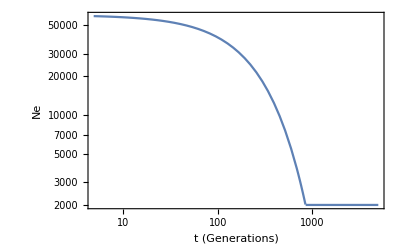

```mathematica
LogLogPlot[NGE,{t,0,5000},AxesOrigin->{0,0},Frame->True,FrameLabel->{"t (Generations)","Ne"}]
```

Equation 4 (distribution of times to coalescence, given the demographic scenario NGE):

```mathematica
qjtGenExp[j_,B_]:=Binomial[j,2]/(B NGE)Exp[-PiecewiseIntegrate[Binomial[j,2]/(B NGE/.t->σ),{σ,0,t}]]
```

```mathematica
qjtGenExp[2,1]
```

(ⅇ^(-If[850==t,493/(1200 Log[30]),0]-If[0<t<850,(17 (-1+30^(t/850)))/(1200 Log[30]),0]-If[850<t,(2465-2550 Log[30]+3 t Log[30])/(6000 Log[30]),0]-If[t<0,(17 (-1+30^(t/850)))/(1200 Log[30]),0]))/Piecewise[{{2^(4+(850-t)/850) 3^((850-t)/850) 5^(3+(850-t)/850), t<850}, {2000, t≥850}, {0, True}}]

Equation 3 (the expectation of equation 4):

```mathematica
ejGenExp[j_,B_]:=PiecewiseIntegrate[t qjtGenExp[j,B],{t,0,∞}]
```

n... sample size, b... allele count, y... original N was N0/y, z... time back to change on units of 2 N0, N0... current effective pop size

Equation 8 (an expression for the probability to see b derived alleles in a sample of n with the effective population size scaled by B):

```mathematica
qnbGenExpL[n_,b_,B_]:=Sum[ejGenExp[j,B]wnbj[n,b,j],{j,2,n}]/Sum[ejGenExp[j,B]vnj[n,j],{j,2,n}]
```

As a test, derive an expression where B is set to 1 (no BGS). This does not have to be executed, and will be replicated in the last section (Including the effects of BGS - Different values of B).

```mathematica
AbsoluteTiming[qnbGenExp20L=Simplify[qnbGenExpL[20,b,1],TimeConstraint->1];]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

{626.721,Null}

Relative site frequencies under the expansion model without BGS. See further down for BGS.

```mathematica
Table[qnbGenExp20L,{b,1,19}]//N
```

{0.536352,0.120582,0.0621538,0.0427046,0.0330783,0.0272213,0.0232155,0.0202722,0.0180048,0.016199,0.0147245,0.0134968,0.0124583,0.0115684,0.0107971,0.0101223,0.00952687,0.0089976,0.00852404}

#### Instantaneous decline

This is analogous to the section above, but adjusted for the decline model.

```mathematica
NeGenStep[anf_,end_,tchange_]:=Piecewise[{{anf,t<tchange},{end,t≥tchange}}]
```

```mathematica
NGS=NeGenStep[2 2100,2 12300,4750]
```

Piecewise[{{4200, t<4750}, {24600, t≥4750}, {0, True}}]

```mathematica
(*NGS=NeGenStep[ 2100, 12300,4750]*)
```

Piecewise[{{2100, t<4750}, {12300, t≥4750}, {0, True}}]

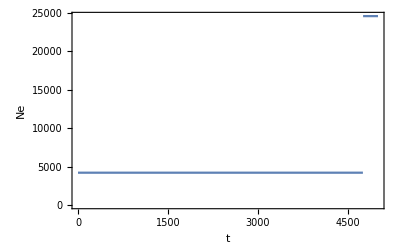

```mathematica
Plot[NGS,{t,0,5000},AxesOrigin->{0,0},Frame->True,FrameLabel->{"t","Ne"}]
```

```mathematica
qjtGenStep[j_,B_]:=Binomial[j,2]/(NGS B)Exp[-PiecewiseIntegrate[Binomial[j,2]/(B NGS/.t->σ),{σ,0,t}]]
```

```mathematica
qjtGenStep[2,1]
```

ⅇ^(-If[4750==t,95/84,0]-If[0<t<4750,t/4200,0]-If[4750<t,(161500+7 t)/172200,0]-If[t<0,t/4200,0])/Piecewise[{{4200, t<4750}, {24600, t≥4750}, {0, True}}]

```mathematica
ejGenStep[j_,B_]:=PiecewiseIntegrate[t qjtGenStep[j,B],{t,0,∞}]
```

n... sample size, b... allele count, y... original N was N0/y, z... time back to change on units of 2 N0, N0... current effective pop size

```mathematica
qnbGenStepL[n_,b_,B_]:=Sum[ejGenStep[j,B]wnbj[n,b,j],{j,2,n}]/Sum[ejGenStep[j,B]vnj[n,j],{j,2,n}]
```

```mathematica
AbsoluteTiming[qnbGenStep20L=Simplify[qnbGenStepL[20,b,1],TimeConstraint->1];]
```

{18.8828,Null}

```mathematica
ByteCount[qnbGenStep20L]
```

71888

```mathematica
Table[qnbGenStep20L,{b,1,19}]//N
```

{0.161012,0.0964657,0.0746265,0.0634678,0.0565841,0.0518402,0.0483211,0.0455693,0.0433305,0.0414522,0.0398374,0.0384213,0.037159,0.0360187,0.0349767,0.0340155,0.0331216,0.0322845,0.0314959}

#### Constant size

```mathematica
qjtGen10k[j_,B_]:=Binomial[j,2]/(2 10000B)Exp[-PiecewiseIntegrate[Binomial[j,2]/(2 10000B),{σ,0,t}]]
```

```mathematica
ejGen10k[j_,B_]:=PiecewiseIntegrate[t qjtGen10k[j,B],{t,0,∞}]
```

n... sample size, b... allele count, y... original N was N0/y, z... time back to change on units of 2 N0, N0... current effective pop size

```mathematica
qnb10kL[n_,b_,B_]:=Sum[ejGen10k[j,B]wnbj[n,b,j],{j,2,n}]/Sum[ejGen10k[j,B]vnj[n,j],{j,2,n}]
```

```mathematica
AbsoluteTiming[qnb10kL20=Simplify[qnb10kL[20,b], TimeConstraint->1];]
```

{3.6226,Null}

```mathematica
AbsoluteTiming[qnb10kL20=Simplify[qnb10kL[20,b,1], TimeConstraint->1]]
```

{3.64444,1/431565146817638400(Binomial[0,-1+b]+Binomial[1,-1+b]+Binomial[2,-1+b]+Binomial[3,-1+b]+Binomial[4,-1+b]+Binomial[5,-1+b]+Binomial[6,-1+b]+Binomial[7,-1+b]+Binomial[8,-1+b]+Binomial[9,-1+b]+Binomial[10,-1+b]+Binomial[11,-1+b]+Binomial[12,-1+b]+Binomial[13,-1+b]+Binomial[14,-1+b]+Binomial[15,-1+b]+Binomial[16,-1+b]+Binomial[17,-1+b]+Binomial[18,-1+b]) (19-b)! (-1+b)!}

```mathematica
Table[qnb10kL20,{b,1,19}]//N
```

{0.28187,0.140935,0.0939565,0.0704674,0.0563739,0.0469783,0.0402671,0.0352337,0.0313188,0.028187,0.0256245,0.0234891,0.0216823,0.0201335,0.0187913,0.0176169,0.0165806,0.0156594,0.0148352}

35 secs

#### Including the effects of BGS - Different values of B

Lines: 1-constant, 2,-decline, 3-growth

```mathematica
bMat=Rationalize[{{1.000,0.716,0.608,0.252,0.534,0.390,0.576},
{1.000,0.609,0.438,0.113,0.358,0.202,0.384},
{1.000,0.886,0.865,0.852,0.865,0.919,0.960}}];
```

```mathematica
bMat//TableForm
```

1 | 179/250 | 76/125 | 63/250 | 267/500 | 39/100 | 72/125
1 | 609/1000 | 219/500 | 113/1000 | 179/500 | 101/500 | 48/125
1 | 443/500 | 173/200 | 213/250 | 173/200 | 919/1000 | 24/25

```mathematica
AbsoluteTiming[termsCons=Table[qnb10kL[20,b,bMat⟦1,k⟧],{k,1,7}];]
```

{23.2029,Null}

```mathematica
AbsoluteTiming[termsStep=Table[qnbGenStepL[20,b,bMat⟦2,k⟧],{k,1,7}];]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

$Aborted

```mathematica
AbsoluteTiming[termsExp=Table[qnbGenExpL[20,b,bMat⟦3,k⟧],{k,1,7}];]
```

{3566.56,Null}

```mathematica
ByteCount[termsCons]
ByteCount[termsStep]
ByteCount[termsExp]
```

809416

901704

1249568

```mathematica
Table[termsCons⟦1⟧,{b,1,19}]//N
```

{0.28187,0.140935,0.0939565,0.0704674,0.0563739,0.0469783,0.0402671,0.0352337,0.0313188,0.028187,0.0256245,0.0234891,0.0216823,0.0201335,0.0187913,0.0176169,0.0165806,0.0156594,0.0148352}

```mathematica
Table[termsCons⟦k⟧,{k,1,7},{b,1,19}]//N//TableForm
```

0.28187 | 0.140935 | 0.0939565 | 0.0704674 | 0.0563739 | 0.0469783 | 0.0402671 | 0.0352337 | 0.0313188 | 0.028187 | 0.0256245 | 0.0234891 | 0.0216823 | 0.0201335 | 0.0187913 | 0.0176169 | 0.0165806 | 0.0156594 | 0.0148352
0.28187 | 0.140935 | 0.0939565 | 0.0704674 | 0.0563739 | 0.0469783 | 0.0402671 | 0.0352337 | 0.0313188 | 0.028187 | 0.0256245 | 0.0234891 | 0.0216823 | 0.0201335 | 0.0187913 | 0.0176169 | 0.0165806 | 0.0156594 | 0.0148352
0.28187 | 0.140935 | 0.0939565 | 0.0704674 | 0.0563739 | 0.0469783 | 0.0402671 | 0.0352337 | 0.0313188 | 0.028187 | 0.0256245 | 0.0234891 | 0.0216823 | 0.0201335 | 0.0187913 | 0.0176169 | 0.0165806 | 0.0156594 | 0.0148352
0.28187 | 0.140935 | 0.0939565 | 0.0704674 | 0.0563739 | 0.0469783 | 0.0402671 | 0.0352337 | 0.0313188 | 0.028187 | 0.0256245 | 0.0234891 | 0.0216823 | 0.0201335 | 0.0187913 | 0.0176169 | 0.0165806 | 0.0156594 | 0.0148352
0.28187 | 0.140935 | 0.0939565 | 0.0704674 | 0.0563739 | 0.0469783 | 0.0402671 | 0.0352337 | 0.0313188 | 0.028187 | 0.0256245 | 0.0234891 | 0.0216823 | 0.0201335 | 0.0187913 | 0.0176169 | 0.0165806 | 0.0156594 | 0.0148352
0.28187 | 0.140935 | 0.0939565 | 0.0704674 | 0.0563739 | 0.0469783 | 0.0402671 | 0.0352337 | 0.0313188 | 0.028187 | 0.0256245 | 0.0234891 | 0.0216823 | 0.0201335 | 0.0187913 | 0.0176169 | 0.0165806 | 0.0156594 | 0.0148352
0.28187 | 0.140935 | 0.0939565 | 0.0704674 | 0.0563739 | 0.0469783 | 0.0402671 | 0.0352337 | 0.0313188 | 0.028187 | 0.0256245 | 0.0234891 | 0.0216823 | 0.0201335 | 0.0187913 | 0.0176169 | 0.0165806 | 0.0156594 | 0.0148352

```mathematica
Table[termsStep⟦1⟧,{b,1,19}]//N
```

{0.161012,0.0964657,0.0746265,0.0634678,0.0565841,0.0518402,0.0483211,0.0455693,0.0433305,0.0414522,0.0398374,0.0384213,0.037159,0.0360187,0.0349767,0.0340155,0.0331216,0.0322845,0.0314959}

```mathematica
Table[termsStep⟦k⟧,{k,1,7},{b,1,19}]//N//TableForm
```

General::munfl: Exp[-1901.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1531.29] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.161012 | 0.0964657 | 0.0746265 | 0.0634678 | 0.0565841 | 0.0518402 | 0.0483211 | 0.0455693 | 0.0433305 | 0.0414522 | 0.0398374 | 0.0384213 | 0.037159 | 0.0360187 | 0.0349767 | 0.0340155 | 0.0331216 | 0.0322845 | 0.0314959
0.198345 | 0.109085 | 0.0792836 | 0.0643471 | 0.0553565 | 0.0493389 | 0.0450202 | 0.0417634 | 0.0392144 | 0.0371611 | 0.0354681 | 0.0340456 | 0.032831 | 0.0317798 | 0.0308594 | 0.0300452 | 0.0293186 | 0.0286649 | 0.0280727
0.231675 | 0.121645 | 0.0849616 | 0.066615 | 0.055603 | 0.0482584 | 0.0430093 | 0.03907 | 0.0360039 | 0.0335491 | 0.0315387 | 0.0298617 | 0.0284412 | 0.0272222 | 0.0261644 | 0.0252376 | 0.0244186 | 0.0236896 | 0.0230362
0.281727 | 0.141288 | 0.0933225 | 0.0709022 | 0.0565139 | 0.0466869 | 0.0401516 | 0.0354205 | 0.0314809 | 0.0281087 | 0.0254465 | 0.0234819 | 0.0218695 | 0.0202199 | 0.0186039 | 0.0175306 | 0.0168813 | 0.0154562 | 0.0149085
0.250643 | 0.128915 | 0.0883379 | 0.0680482 | 0.0558737 | 0.0477566 | 0.0419582 | 0.0376089 | 0.0342256 | 0.0315186 | 0.0293035 | 0.0274572 | 0.0258946 | 0.024555 | 0.0233937 | 0.0223774 | 0.0214804 | 0.0206828 | 0.019969
0.278758 | 0.139736 | 0.0933955 | 0.070226 | 0.0563218 | 0.0470571 | 0.0404327 | 0.0354709 | 0.0316087 | 0.0285171 | 0.0259922 | 0.0238849 | 0.0221009 | 0.0205762 | 0.0192495 | 0.0180926 | 0.0170697 | 0.0161612 | 0.0153482
0.244425 | 0.126527 | 0.0872258 | 0.0675731 | 0.0557801 | 0.0479169 | 0.0422993 | 0.0380852 | 0.0348068 | 0.0321833 | 0.0300362 | 0.0282463 | 0.0267312 | 0.0254321 | 0.0243057 | 0.0233196 | 0.0224491 | 0.021675 | 0.0209819

```mathematica
Table[termsExp⟦1⟧,{b,1,19}]//N
```

{0.536352,0.120582,0.0621538,0.0427046,0.0330783,0.0272213,0.0232155,0.0202722,0.0180048,0.016199,0.0147245,0.0134968,0.0124583,0.0115684,0.0107971,0.0101223,0.00952687,0.0089976,0.00852404}

```mathematica
Table[termsExp⟦k⟧,{k,1,7},{b,1,19}]//N//TableForm
```

0.536352 | 0.120582 | 0.0621538 | 0.0427046 | 0.0330783 | 0.0272213 | 0.0232155 | 0.0202722 | 0.0180048 | 0.016199 | 0.0147245 | 0.0134968 | 0.0124583 | 0.0115684 | 0.0107971 | 0.0101223 | 0.00952687 | 0.0089976 | 0.00852404
0.547501 | 0.121881 | 0.061313 | 0.0414668 | 0.0318478 | 0.0260947 | 0.0222058 | 0.0193694 | 0.0171939 | 0.0154655 | 0.0140561 | 0.0128835 | 0.011892 | 0.0110424 | 0.0103062 | 0.00966201 | 0.00909365 | 0.00858844 | 0.00813642
0.549625 | 0.122173 | 0.0611699 | 0.0412348 | 0.0316111 | 0.0258751 | 0.0220076 | 0.0191914 | 0.0170336 | 0.0153203 | 0.0139237 | 0.0127619 | 0.0117797 | 0.0109381 | 0.0102088 | 0.00957075 | 0.00900776 | 0.00850733 | 0.00805957
0.550951 | 0.122363 | 0.0610838 | 0.0410907 | 0.031463 | 0.0257373 | 0.0218829 | 0.0190793 | 0.0169326 | 0.0152288 | 0.0138402 | 0.0126852 | 0.0117089 | 0.0108723 | 0.0101474 | 0.00951317 | 0.00895356 | 0.00845614 | 0.00801108
0.549625 | 0.122173 | 0.0611699 | 0.0412348 | 0.0316111 | 0.0258751 | 0.0220076 | 0.0191914 | 0.0170336 | 0.0153203 | 0.0139237 | 0.0127619 | 0.0117797 | 0.0109381 | 0.0102088 | 0.00957075 | 0.00900776 | 0.00850733 | 0.00805957
0.544206 | 0.121458 | 0.0615464 | 0.0418293 | 0.0322135 | 0.026432 | 0.0225094 | 0.0196415 | 0.0174387 | 0.0156871 | 0.0142581 | 0.0130688 | 0.0120632 | 0.0112014 | 0.0104546 | 0.00980115 | 0.00922461 | 0.00871213 | 0.0082536
0.540189 | 0.120988 | 0.0618486 | 0.0422753 | 0.0326571 | 0.0268383 | 0.0228735 | 0.0199671 | 0.0177312 | 0.0159516 | 0.0144992 | 0.0132901 | 0.0122674 | 0.0113911 | 0.0106317 | 0.00996718 | 0.00938087 | 0.00885971 | 0.00839341

Nucleotide diversity (expected branch lengths of a sample of 2)

```mathematica
pis=Table[2 10^-8{ejGen10k,ejGenStep,ejGenExp}⟦l⟧[2,bMat⟦l,k⟧],{k,1,7},{l,1,3}];//AbsoluteTiming
```

{78.7298,Null}

```mathematica
pis//Transpose//N//TableForm//ScientificForm
```

4.×10^-4 | 2.864×10^-4 | 2.432×10^-4 | 1.008×10^-4 | 2.136×10^-4 | 1.56×10^-4 | 2.304×10^-4
2.15672×10^-4 | 8.995×10^-5 | 5.03049×10^-5 | 9.49408×10^-6 | 3.62745×10^-5 | 1.72731×10^-5 | 4.04957×10^-5
5.19325×10^-5 | 4.73429×10^-5 | 4.64966×10^-5 | 4.59726×10^-5 | 4.64966×10^-5 | 4.86722×10^-5 | 5.03229×10^-5

#### Post-burn-in values of B

The  genetic diversity at the end of the simulations is still more or less in-line with the levels of BGS before the demographic change started. Using values of B obtained from the simulations (after burn-in, but before population size change), allows good predictions of the final levels of nucleotide diversity and B.

```mathematica
bPostBurnIn=Rationalize[{{1.000,0.716,0.602,0.253,0.540,0.388,0.568},
{1.000,0.710,0.602,0.252,0.538,0.386,0.568},
{1.000,0.856,0.827,0.790,0.850,0.871,0.920}}];
```

```mathematica
bPostBurnIn//TableForm
```

1 | 179/250 | 301/500 | 253/1000 | 27/50 | 97/250 | 71/125
1 | 71/100 | 301/500 | 63/250 | 269/500 | 193/500 | 71/125
1 | 107/125 | 827/1000 | 79/100 | 17/20 | 871/1000 | 23/25

Derive expressions for the site-frequency spectra (depending on B) for each demographic scenario:

```mathematica
AbsoluteTiming[termsConsPBI=Table[qnb10kL[20,b,bPostBurnIn⟦1,k⟧],{k,1,7}];]
```

{25.4276,Null}

```mathematica
AbsoluteTiming[termsStepPBI=Table[qnbGenStepL[20,b,bPostBurnIn⟦2,k⟧],{k,1,7}];]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

{428.134,Null}

```mathematica
AbsoluteTiming[termsExpPBI=Table[qnbGenExpL[20,b,bPostBurnIn⟦3,k⟧],{k,1,7}];]
```

{3596.29,Null}

```mathematica
ByteCount[termsConsPBI]
ByteCount[termsStepPBI]
ByteCount[termsExpPBI]
```

810096

899624

1258968

Get site-frequency spectra for a sample of size 20 (constant, step decline, exponential expansion). Rows: neutral, DFE1, DFE2, DFE3, DFE4, DFE5, DFE6. Cols: Frequency clesses 1-19

```mathematica
Table[termsConsPBI⟦k⟧,{k,1,7},{b,1,19}]//N//TableForm
```

0.28187 | 0.140935 | 0.0939565 | 0.0704674 | 0.0563739 | 0.0469783 | 0.0402671 | 0.0352337 | 0.0313188 | 0.028187 | 0.0256245 | 0.0234891 | 0.0216823 | 0.0201335 | 0.0187913 | 0.0176169 | 0.0165806 | 0.0156594 | 0.0148352
0.28187 | 0.140935 | 0.0939565 | 0.0704674 | 0.0563739 | 0.0469783 | 0.0402671 | 0.0352337 | 0.0313188 | 0.028187 | 0.0256245 | 0.0234891 | 0.0216823 | 0.0201335 | 0.0187913 | 0.0176169 | 0.0165806 | 0.0156594 | 0.0148352
0.28187 | 0.140935 | 0.0939565 | 0.0704674 | 0.0563739 | 0.0469783 | 0.0402671 | 0.0352337 | 0.0313188 | 0.028187 | 0.0256245 | 0.0234891 | 0.0216823 | 0.0201335 | 0.0187913 | 0.0176169 | 0.0165806 | 0.0156594 | 0.0148352
0.28187 | 0.140935 | 0.0939565 | 0.0704674 | 0.0563739 | 0.0469783 | 0.0402671 | 0.0352337 | 0.0313188 | 0.028187 | 0.0256245 | 0.0234891 | 0.0216823 | 0.0201335 | 0.0187913 | 0.0176169 | 0.0165806 | 0.0156594 | 0.0148352
0.28187 | 0.140935 | 0.0939565 | 0.0704674 | 0.0563739 | 0.0469783 | 0.0402671 | 0.0352337 | 0.0313188 | 0.028187 | 0.0256245 | 0.0234891 | 0.0216823 | 0.0201335 | 0.0187913 | 0.0176169 | 0.0165806 | 0.0156594 | 0.0148352
0.28187 | 0.140935 | 0.0939565 | 0.0704674 | 0.0563739 | 0.0469783 | 0.0402671 | 0.0352337 | 0.0313188 | 0.028187 | 0.0256245 | 0.0234891 | 0.0216823 | 0.0201335 | 0.0187913 | 0.0176169 | 0.0165806 | 0.0156594 | 0.0148352
0.28187 | 0.140935 | 0.0939565 | 0.0704674 | 0.0563739 | 0.0469783 | 0.0402671 | 0.0352337 | 0.0313188 | 0.028187 | 0.0256245 | 0.0234891 | 0.0216823 | 0.0201335 | 0.0187913 | 0.0176169 | 0.0165806 | 0.0156594 | 0.0148352

```mathematica
Table[termsStepPBI⟦k⟧,{k,1,7},{b,1,19}]//N//TableForm
```

General::munfl: Exp[-852.702] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.161012 | 0.0964657 | 0.0746265 | 0.0634678 | 0.0565841 | 0.0518402 | 0.0483211 | 0.0455693 | 0.0433305 | 0.0414522 | 0.0398374 | 0.0384213 | 0.037159 | 0.0360187 | 0.0349767 | 0.0340155 | 0.0331216 | 0.0322845 | 0.0314959
0.184488 | 0.104069 | 0.0771662 | 0.063643 | 0.0554717 | 0.0499766 | 0.0460109 | 0.0430012 | 0.0406289 | 0.038703 | 0.0371017 | 0.0357441 | 0.0345739 | 0.0335512 | 0.0326464 | 0.0318375 | 0.0311077 | 0.0304439 | 0.0298356
0.199456 | 0.109495 | 0.0794627 | 0.0644126 | 0.0553555 | 0.0492949 | 0.0449466 | 0.0416685 | 0.039104 | 0.0370389 | 0.0353371 | 0.0339078 | 0.0326881 | 0.0316331 | 0.0307098 | 0.0298937 | 0.0291658 | 0.0285114 | 0.0279189
0.272676 | 0.137393 | 0.0922993 | 0.0697523 | 0.0562239 | 0.0472054 | 0.0407627 | 0.035932 | 0.0321734 | 0.0291674 | 0.026708 | 0.0246575 | 0.0229239 | 0.0214366 | 0.0201485 | 0.0190209 | 0.0180262 | 0.017142 | 0.0163508
0.210618 | 0.113657 | 0.0813119 | 0.0651207 | 0.0553911 | 0.0488923 | 0.0442396 | 0.0407409 | 0.0380113 | 0.0358203 | 0.0340209 | 0.0325152 | 0.0312355 | 0.0301333 | 0.0291731 | 0.0283283 | 0.0275786 | 0.0269081 | 0.0263043
0.243946 | 0.126343 | 0.0871402 | 0.0675367 | 0.0557731 | 0.0479294 | 0.0423257 | 0.038122 | 0.0348516 | 0.0322346 | 0.0300927 | 0.0283071 | 0.0267957 | 0.0254996 | 0.0243759 | 0.0233921 | 0.0225236 | 0.0217513 | 0.0210598
0.205157 | 0.111612 | 0.0803968 | 0.0647641 | 0.0553643 | 0.0490811 | 0.0445788 | 0.0411896 | 0.0385424 | 0.0364147 | 0.0346648 | 0.0331982 | 0.0319496 | 0.0308723 | 0.029932 | 0.029103 | 0.0283658 | 0.0277049 | 0.0271085

```mathematica
Table[termsExpPBI⟦k⟧,{k,1,7},{b,1,19}]//N//TableForm
```

0.536352 | 0.120582 | 0.0621538 | 0.0427046 | 0.0330783 | 0.0272213 | 0.0232155 | 0.0202722 | 0.0180048 | 0.016199 | 0.0147245 | 0.0134968 | 0.0124583 | 0.0115684 | 0.0107971 | 0.0101223 | 0.00952687 | 0.0089976 | 0.00852404
0.550542 | 0.122304 | 0.0611101 | 0.0411351 | 0.0315087 | 0.0257799 | 0.0219215 | 0.019114 | 0.0169638 | 0.0152571 | 0.013866 | 0.012709 | 0.0117308 | 0.0108926 | 0.0101664 | 0.00953098 | 0.00897032 | 0.00847197 | 0.00802608
0.553521 | 0.122749 | 0.0609239 | 0.0408132 | 0.0311752 | 0.0254682 | 0.0216388 | 0.0188594 | 0.0167342 | 0.0150489 | 0.0136761 | 0.0125345 | 0.0115696 | 0.010743 | 0.0100267 | 0.00939998 | 0.00884703 | 0.00835553 | 0.00791576
0.557373 | 0.123376 | 0.0607031 | 0.0404019 | 0.0307418 | 0.0250599 | 0.0212667 | 0.0185234 | 0.0164305 | 0.0147732 | 0.0134244 | 0.0123033 | 0.011356 | 0.0105445 | 0.00984142 | 0.00922629 | 0.00868355 | 0.00820113 | 0.00776949
0.551155 | 0.122393 | 0.0610707 | 0.0410685 | 0.0314402 | 0.025716 | 0.0218636 | 0.0190619 | 0.0169169 | 0.0152146 | 0.0138272 | 0.0126733 | 0.0116979 | 0.0108621 | 0.0101379 | 0.00950423 | 0.00894515 | 0.0084482 | 0.00800355
0.549016 | 0.122088 | 0.0612103 | 0.0413011 | 0.031679 | 0.0259382 | 0.0220647 | 0.0192427 | 0.0170798 | 0.0153622 | 0.0139619 | 0.012797 | 0.011812 | 0.0109681 | 0.0102369 | 0.00959705 | 0.00903251 | 0.0085307 | 0.00808172
0.544107 | 0.121446 | 0.0615537 | 0.0418403 | 0.0322244 | 0.026442 | 0.0225184 | 0.0196496 | 0.0174459 | 0.0156937 | 0.0142641 | 0.0130744 | 0.0120683 | 0.0112061 | 0.010459 | 0.00980529 | 0.00922851 | 0.00871581 | 0.00825708

Nucleotide diversity (expected branch lengths of a sample of 2)

```mathematica
pisPBI=Table[2 10^-8{ejGen10k,ejGenStep,ejGenExp}⟦l⟧[2,bPostBurnIn⟦l,k⟧],{k,1,7},{l,1,3}];//AbsoluteTiming
```

{83.47,Null}

Nucleotide diversity expected after demographic change using values of B from simulations (obtained after burn-in, but before demographic change)

```mathematica
pisPBI//Transpose//N//TableForm//ScientificForm
```

4.×10^-4 | 2.864×10^-4 | 2.408×10^-4 | 1.012×10^-4 | 2.16×10^-4 | 1.552×10^-4 | 2.272×10^-4
2.15672×10^-4 | 1.18543×10^-4 | 8.80969×10^-5 | 2.23241×10^-5 | 7.20142×10^-5 | 4.0834×10^-5 | 7.93551×10^-5
5.19325×10^-5 | 4.61338×10^-5 | 4.49645×10^-5 | 4.34715×10^-5 | 4.5892×10^-5 | 4.67384×10^-5 | 4.87125×10^-5

Corresponding final values of B

```mathematica
Map[#/#⟦1⟧&,pisPBI//Transpose]//N//TableForm
```

1. | 0.716 | 0.602 | 0.253 | 0.54 | 0.388 | 0.568
1. | 0.549643 | 0.408476 | 0.103509 | 0.333906 | 0.189334 | 0.367943
1. | 0.888342 | 0.865825 | 0.837078 | 0.883684 | 0.899984 | 0.937996